```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

P::shdw: Symbol P appears in multiple contexts {defs448`,Global`}; definitions in context defs448` may shadow or be shadowed by other definitions.

#### 449 HW 7 Celeste Keith

#### 3. 14.11

We know V=-e  E(t)  ⟨1s|z|2p⟩=-e E(r) ∫dr P_(1s)r P_(2p)∫ⅆΩ , and that Y_00 √((4π)/3)Y_10 Y_10=-(e E(t))/(√3)∫drP_(1s)r P_(2p)

```mathematica
Integrate[Subscript[P, 1,0][r]r Subscript[P, 2,1][r],{r,0,∞}]/√3
```

(128 √2)/243

```mathematica
%//N
```

0.744936

We now use a fourier transform:

```mathematica
Integrate[ⅇ^(-t/τ)ⅇ^(-ⅈ ω t),{t,0,∞},Assumptions->{τ>0,ω>0}]
```

(ⅈ τ)/(ⅈ-τ ω)

```mathematica
% %^*//Simplify
```

τ^2/(1+τ^2 ω^2)

(e^2(E_0^2(.74 a_0))^2)/ℏ^2 τ^2/(1+ω^2 τ^2)  where ℏω=E_(2p)-E_(1p)
=-1/2-(-1/8)
=-3/8 hartrees

#### 4. An electron is confined in a spherical box

We have that our ground state is E_s=p^2/(2m)=1/(2m)(ℏ^2(π/a))^2=(π^2 ℏ^2)/(2 m a^2) 
 P_s=√(2/a)sin[π r/a]

For the p state:

```mathematica
DSolve[{-ℏ^2/(2m)p''[r]+(2 ℏ^2)/(2 m r^2)p[r]==(ℏ^2 k^2)/(2 m) p[r],p[0]==0},p[r],r]//PowerExpand
```

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{p[r]→-(√(2/π) C[1] (k r Cos[k r]-Sin[k r]))/(k^(3/2) r)}}

We have that our quantization, k*a, will be equal to tan(k*a). We plot here, and then find the root:

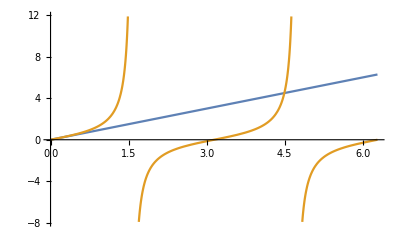

```mathematica
Plot[{ka,Tan[ka]},{ka,0,2π}]
```

```mathematica
FindRoot[ka==Tan[ka],{ka,4}]
```

{ka→4.49341}

So, we have that our  E_p=ℏ^2/(2m a^2)4.493^2. We now find our energy of the s state and subtract the two:

E_p-E_s=ℏ^2/(2m a^2)(4.493^2-π^2)

This is found to be about 1eV.

```mathematica
$Assumptions=a>0;
Integrate[p[r]^2/.p[r]->-(√(2/π) C[1] (k r Cos[k r]-Sin[k r]))/(k^(3/2) r),{r,0,a}]/. k-> 4.493/a
```

0.0675086 a^2 C[1]^2

We then have that so P_p[r]=-(√(2/π) C[1] (k r Cos[k r]-Sin[k r]))/(k^(3/2) r). We define our P_p:

```mathematica
Pp[r_]:=-(√(2/π) C[1] (k r Cos[k r]-Sin[k r]))/(k^(3/2) r)/.{k-> 4.493/a,C[1]->1/(√(0.0675086443552605 a^2))}
```

We then choose the m=0 state in order to calculate Γ. We use the fact that ∫ⅆΩ Y_00 cosθ Y_10=Y_00 √(4 π/3)∫Y_10 Y_10 ⅆΩ=√(1/3)

```mathematica
(4 e^2  ω^3)/(3 c^3  ℏ)rmat^2//.{rmat->√(1/3) Integrate[√(2/a)Sin[π r/a]r Pp[r],{r,0,a}], a-> √((ℏ^2 (4.493^2-π^2))/(2 m ℏ ω))}
```

(0.644223 e^2 ω^2)/(c^3 m)

```mathematica
%//.{e->√(14.4 eV Å), m-> 511000 eV/c^2,ω-> (1 eV)/ℏ,ℏ-> 1973 eV Å/c,c-> 3 10^18 Å/sec}
```

(1.39909×10^7)/sec

We then find the lifetime:

```mathematica
1/((1.3990879253287021*^7)/sec)
```

7.14751×10^-8 sec

#### 5.

```mathematica
{1,0}.MatrixExp[-ⅈ ({{0, √n Ω/2}, {√n Ω/2, -Δ}})t].{1,0}//ExpToTrig//Simplify
```

{{((Cos[(t Δ)/2]+ⅈ Sin[(t Δ)/2]) (√(Δ^2+n Ω^2) Cos[1/2 t √(Δ^2+n Ω^2)]-ⅈ Δ Sin[1/2 t √(Δ^2+n Ω^2)]))/(√(Δ^2+n Ω^2))}}

```mathematica
% %^*//FullSimplify//MF
```

(((2 Δ^2+n Ω^2+n Ω^2 Cos[t √(Δ^2+n Ω^2)])^4)/(16 (Δ^2+n Ω^2)^4))

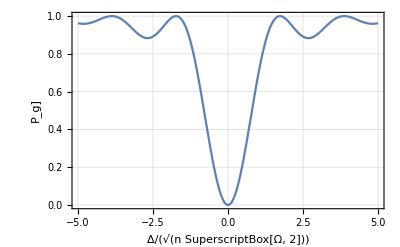

```mathematica
ThadPlot[(2 Δ^2+n Ω^2+n Ω^2 Cos[t √(Δ^2+n Ω^2)])/(2 Δ^2+2 n Ω^2)//.{t-> π/(√(n Ω^2)),n Ω^2->1},{Δ,-5,5},{},{"Δ/(√(n SuperscriptBox[Ω, 2]))","P_g]"}]
```

#### 6.

```mathematica
{1,0}.MatrixExp[-ⅈ({{0, √n Ω/2}, {√n Ω/2, -Δ}}/.{Δ->0,n->0})t].{1,0}//ExpToTrig//FullSimplify
```

{{1}}

```mathematica
Abs[{1,0}.MatrixExp[-ⅈ({{0, √n Ω/2}, {√n Ω/2, -Δ}}/.{Δ->0,n->0})t].{1,0}]^2//ExpToTrig//FullSimplify
```

{{1}}